```mathematica
f0[x_,theta_]:=1/theta*Exp[-x/theta];
f[x_,theta_,c_,eps_]:=(1-eps)*f0[x,theta]+eps*f0[x,c];
Lq[u_,q_]:=(u^(1-q)-1)/(1-q);
(*phi[x_,theta_,q_]:=D[Lq[f0[x,theta],q],theta];*)
phi[x_,theta_,q_]:=((ⅇ^(-x/theta)/theta)^(1-q) (-theta+x))/theta^2;
(*phip[x_,theta_,q_]:=D[Lq[f0[x,theta],q],theta,theta];*)
phip[x_,theta_,q_]:=((ⅇ^(-x/theta)/theta)^(1-q) (-(-2+q) theta^2+2 (-2+q) theta x-(-1+q) x^2))/theta^4;
```

```mathematica
Integrate[(phi[x,thetaP,q])*f[x,theta0,c,eps],{x,0,Infinity},Assumptions->{thetaP∈Reals,thetaP>0,theta0∈Reals,theta0>0,eps∈Reals,eps≥0,eps≤1,q∈Reals,q≥0,q≤1,c∈Reals,c>0}]
```

thetaP^(-1+q) ((c eps)/(c-c q+thetaP)^2-eps/(c-c q+thetaP)-((-1+eps) theta0)/(theta0-q theta0+thetaP)^2+(-1+eps)/(theta0-q theta0+thetaP))

```mathematica
Collect[c eps(theta0-q theta0+thetaP)^2-eps(c-c q+thetaP)(theta0-q theta0+thetaP)^2-(-1+eps) theta0(c-c q+thetaP)^2+(-1+eps)(theta0-q theta0+thetaP)(c-c q+thetaP)^2,thetaP]
```

c^2 (1-eps) theta0+c^2 (-1+eps) theta0-2 c^2 (1-eps) q theta0-3 c^2 (-1+eps) q theta0+c^2 (1-eps) q^2 theta0+3 c^2 (-1+eps) q^2 theta0-c^2 (-1+eps) q^3 theta0+c eps q theta0^2-2 c eps q^2 theta0^2+c eps q^3 theta0^2+(c^2 (-1+eps)-2 c^2 (-1+eps) q+c^2 (-1+eps) q^2+2 c (1-eps) theta0+2 c (-1+eps) theta0-2 c (1-eps) q theta0-4 c (-1+eps) q theta0+2 c eps q theta0+2 c (-1+eps) q^2 theta0-2 c eps q^2 theta0-eps theta0^2+2 eps q theta0^2-eps q^2 theta0^2) thetaP+(2 c (-1+eps)-2 c (-1+eps) q+c eps q+(1-eps) theta0+(-1+eps) theta0-2 eps theta0+(1-eps) q theta0+2 eps q theta0) thetaP^2-thetaP^3

```mathematica
aTmp[theta0_,q_,c_,eps_]:=-1;
bTmp[theta0_,q_,c_,eps_]:=c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0;
cTmp[theta0_,q_,c_,eps_]:=(-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2);
dTmp[theta0_,q_,c_,eps_]:=-c (-1+q)^2 q theta0 (c (-1+eps)-eps theta0);
pTmp[theta0_,q_,c_,eps_]:=-bTmp[theta0,q,c,eps]/3/aTmp[theta0,q,c,eps];
(*qTmp[theta0_,q_,c_,eps_]:=(pTmp[theta0,q,c,eps])^3+(bTmp[theta0,q,c,eps]*cTmp[theta0,q,c,eps]-3aTmp[theta0,q,c,eps]*dTmp[theta0,q,c,eps])/(6*(aTmp[theta0,q,c,eps])^2);*)
qTmp[theta0_,q_,c_,eps_]:=1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2));
rTmp[theta0_,q_,c_,eps_]:=cTmp[theta0,q,c,eps]/3/aTmp[theta0,q,c,eps];
thetaP[theta0_,q_,c_,eps_]:=CubeRoot[qTmp[theta0,q,c,eps]+(qTmp[theta0,q,c,eps]^2+(rTmp[theta0,q,c,eps]-pTmp[theta0,q,c,eps]^2)^3)^(1/2)]+CubeRoot[qTmp[theta0,q,c,eps]-(qTmp[theta0,q,c,eps]^2+(rTmp[theta0,q,c,eps]-pTmp[theta0,q,c,eps]^2)^3)^(1/2)]+pTmp[theta0,q,c,eps];
```

```mathematica
thetaP[theta0,1,c,eps]
```

1/3 (c eps+(1-eps) theta0)+2/3 ((c eps+(1-eps) theta0)^3)^(1/3)

```mathematica
thetaP[theta0,q,c,eps]
```

1/3 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))-√((-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2-1/3 (-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))^3+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2)))^2))^(1/3)+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))+√((-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2-1/3 (-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))^3+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2)))^2))^(1/3)

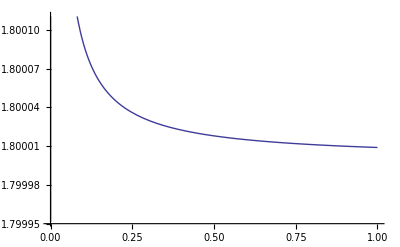

```mathematica
Plot[thetaP[theta0,q,c,eps]/.{theta0->2,q->0.9,c->c0,eps->0.2},{c0,1,10000000}]
```

```mathematica
Simplify[D[thetaP[theta0,q,c,eps],c],Assumptions->{theta0∈Reals,theta0>0,eps∈Reals,eps≥0,eps≤1,q∈Reals,q≥0,q≤1,c∈Reals,c>0}]
```

1/3 (-2+2 eps+2 q-eps q)+(1/9 (-2+2 eps+2 q-eps q) (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2+1/6 (-1+q) (-3 c (-1+eps) (-1+q) q theta0-3 (-1+q) q theta0 (c (-1+eps)-eps theta0)+(2 c (-1+eps) (-1+q)-2 q theta0) (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)+(-2+2 eps+2 q-eps q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))-(3 (-1/3 (-1+q) (2 c (-1+eps) (-1+q)-2 q theta0)-2/9 (-2+2 eps+2 q-eps q) (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)) (-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2-1/3 (-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))^2+2 (1/9 (-2+2 eps+2 q-eps q) (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2+1/6 (-1+q) (-3 c (-1+eps) (-1+q) q theta0-3 (-1+q) q theta0 (c (-1+eps)-eps theta0)+(2 c (-1+eps) (-1+q)-2 q theta0) (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)+(-2+2 eps+2 q-eps q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))) (1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))))/(2 √((-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2-1/3 (-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))^3+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2)))^2)))/(3 ((1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))-√((-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2-1/3 (-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))^3+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2)))^2))^(1/3))^2)+(1/9 (-2+2 eps+2 q-eps q) (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2+1/6 (-1+q) (-3 c (-1+eps) (-1+q) q theta0-3 (-1+q) q theta0 (c (-1+eps)-eps theta0)+(2 c (-1+eps) (-1+q)-2 q theta0) (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)+(-2+2 eps+2 q-eps q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))+(3 (-1/3 (-1+q) (2 c (-1+eps) (-1+q)-2 q theta0)-2/9 (-2+2 eps+2 q-eps q) (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)) (-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2-1/3 (-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))^2+2 (1/9 (-2+2 eps+2 q-eps q) (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2+1/6 (-1+q) (-3 c (-1+eps) (-1+q) q theta0-3 (-1+q) q theta0 (c (-1+eps)-eps theta0)+(2 c (-1+eps) (-1+q)-2 q theta0) (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)+(-2+2 eps+2 q-eps q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))) (1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))))/(2 √((-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2-1/3 (-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))^3+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2)))^2)))/(3 ((1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))+√((-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2-1/3 (-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))^3+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2)))^2))^(1/3))^2)

```mathematica
Limit[thetaP[theta0,q,c,eps],c->Infinity,Assumptions->{theta0∈Reals,theta0>0,eps∈Reals,eps≥0,eps≤1,q∈Reals,q≥0,q≤1,c∈Reals,c>0}]
```

Limit[1/3 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))-√((-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2-1/3 (-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))^3+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2)))^2))^(1/3)+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))+√((-1/9 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^2-1/3 (-1+q) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2))^3+(1/27 (c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0)^3+1/6 (-1+q) (-3 c (-1+q) q theta0 (c (-1+eps)-eps theta0)+(c (-2+2 eps+2 q-eps q)+(eps (-2+q)+q) theta0) (c^2 (-1+eps) (-1+q)-2 c q theta0-eps (-1+q) theta0^2)))^2))^(1/3),c→∞,Assumptions→{theta0∈Reals,theta0>0,eps∈Reals,eps≥0,eps≤1,q∈Reals,q≥0,q≤1,c∈Reals,c>0}]

```mathematica
Integrate[x^2*f[x,theta,c,eps],{x,a,Infinity},Assumptions->{theta∈Reals,theta>0,eps∈Reals,eps≥0,eps≤1,c∈Reals,c>0}]
```

(a^2+2 a c+2 c^2) ⅇ^(-a/c) eps+ⅇ^(-a/theta) (a^2+2 a theta+2 theta^2)-ⅇ^(-a/theta) eps (a^2+2 a theta+2 theta^2)

```mathematica
FullSimplify[(a^2+2 a c+2 c^2) ⅇ^(-a/c) eps+ⅇ^(-a/theta) (a^2+2 a theta+2 theta^2)-ⅇ^(-a/theta) eps (a^2+2 a theta+2 theta^2)]
```

ⅇ^(-a (1/c+1/theta)) ((a^2+2 a c+2 c^2) ⅇ^(a/theta) eps-ⅇ^(a/c) (-1+eps) (a^2+2 a theta+2 theta^2))

```mathematica
Integrate[(x+M)^2*f[x,theta,c,eps],{x,a,Infinity},Assumptions->{theta∈Reals,theta>0,eps∈Reals,eps≥0,eps≤1,c∈Reals,c>0}]
```

ⅇ^(-a (1/c+1/theta)) (ⅇ^(a/theta) eps (a^2+2 c^2+2 c M+M^2+2 a (c+M))-ⅇ^(a/c) (-1+eps) ((a+M)^2+2 (a+M) theta+2 theta^2))

```mathematica
FullSimplify[ⅇ^(-a (1/c+1/theta)) (ⅇ^(a/theta) eps (a^2+2 c^2+2 c M+M^2+2 a (c+M))-ⅇ^(a/c) (-1+eps) ((a+M)^2+2 (a+M) theta+2 theta^2))]
```

ⅇ^(-a (1/c+1/theta)) (ⅇ^(a/theta) eps (a^2+2 c^2+2 c M+M^2+2 a (c+M))-ⅇ^(a/c) (-1+eps) ((a+M)^2+2 (a+M) theta+2 theta^2))

```mathematica
FullSimplify[(a^2+2 a c+2 c^2) ⅇ^(-a/c) eps+ⅇ^(-a/theta) (a^2+2 a theta+2 theta^2)-ⅇ^(-a/theta) eps (a^2+2 a theta+2 theta^2)+ⅇ^(-a (1/c+1/theta)) (ⅇ^(a/theta) eps (a^2+2 c^2+2 c M+M^2+2 a (c+M))-ⅇ^(a/c) (-1+eps) ((a+M)^2+2 (a+M) theta+2 theta^2))]
```

ⅇ^(-(2 a (c+theta))/(c theta)) (ⅇ^(a (1/c+2/theta)) eps (2 (a^2+2 a c+2 c^2)+2 (a+c) M+M^2)-ⅇ^(a (2/c+1/theta)) (-1+eps) (2 a^2+M^2+2 M theta+4 theta^2+2 a (M+2 theta)))

```mathematica
G[a_]:=Exp[-a/R]*(2*a^2+2*a*(M+2*R)+M^2+2*M*R+4*R^2);
```

```mathematica
D[G[a],a]
```

ⅇ^(-a/R) (4 a+2 (M+2 R))-(ⅇ^(-a/R) (2 a^2+M^2+2 M R+4 R^2+2 a (M+2 R)))/R

```mathematica
Solve[D[G[a],a]==0,a]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{a→(-1/2-ⅈ/2) M},{a→(-1/2+ⅈ/2) M}}

```mathematica
FullSimplify[D[G[a],a]/.a->0]
```

-M^2/R

```mathematica
FullSimplify[D[G[a],a]/.a->n^2]
```

-(ⅇ^(-n^2/R) (M^2+2 M n^2+2 n^4))/R

```mathematica
G[n^2]
```

ⅇ^(-n^2/R) (M^2+2 n^4+2 M R+4 R^2+2 n^2 (M+2 R))

```mathematica
Simplify[2*G[a]]
```

2 ⅇ^(-a/R) (2 a^2+M^2+2 M R+4 R^2+2 a (M+2 R))

```mathematica
Integrate[x^2*f[x,theta,c,eps],{x,a,Infinity},Assumptions->{theta∈Reals,theta>0,eps∈Reals,eps≥0,eps≤1,c∈Reals,c>0}]
```

(a^2+2 a c+2 c^2) ⅇ^(-a/c) eps+ⅇ^(-a/theta) (a^2+2 a theta+2 theta^2)-ⅇ^(-a/theta) eps (a^2+2 a theta+2 theta^2)

```mathematica
EA2I=FullSimplify[(a^2+2 a c+2 c^2) ⅇ^(-a/c) eps+ⅇ^(-a/theta) (a^2+2 a theta+2 theta^2)-ⅇ^(-a/theta) eps (a^2+2 a theta+2 theta^2)]
```

ⅇ^(-a (1/c+1/theta)) ((a^2+2 a c+2 c^2) ⅇ^(a/theta) eps-ⅇ^(a/c) (-1+eps) (a^2+2 a theta+2 theta^2))

```mathematica
Integrate[x*f[x,theta,c,eps],{x,a,Infinity},Assumptions->{theta∈Reals,theta>0,eps∈Reals,eps≥0,eps≤1,c∈Reals,c>0}]
```

(a+c) ⅇ^(-a/c) eps+ⅇ^(-a/theta) (a+theta)-ⅇ^(-a/theta) eps (a+theta)

```mathematica
EAI=FullSimplify[(a+c) ⅇ^(-a/c) eps+ⅇ^(-a/theta) (a+theta)-ⅇ^(-a/theta) eps (a+theta)]
```

(a+c) ⅇ^(-a/c) eps-ⅇ^(-a/theta) (-1+eps) (a+theta)

```mathematica
EA2=Integrate[x^2*f[x,theta,c,eps],{x,0,Infinity},Assumptions->{theta∈Reals,theta>0,eps∈Reals,eps≥0,eps≤1,c∈Reals,c>0}]
```

2 (c^2 eps-(-1+eps) theta^2)

```mathematica
EA=Integrate[x*f[x,theta,c,eps],{x,0,Infinity},Assumptions->{theta∈Reals,theta>0,eps∈Reals,eps≥0,eps≤1,c∈Reals,c>0}]
```

c eps+theta-eps theta

```mathematica
PA=Integrate[f[x,theta,c,eps],{x,a,Infinity},Assumptions->{theta∈Reals,theta>0,eps∈Reals,eps≥0,eps≤1,c∈Reals,c>0}]
```

-ⅇ^(-a/theta) (-1+eps)+ⅇ^(-a/c) eps

```mathematica
FullSimplify[4*EA2I+4*(m-1)*EA2*PA+4*R*EAI+2*R*(m-1)*EA*PA+2*R^2*m*PA]
```

2 (-ⅇ^(-a/theta) (-1+eps)+ⅇ^(-a/c) eps) m R^2+2 (-ⅇ^(-a/theta) (-1+eps)+ⅇ^(-a/c) eps) (-1+m) R (c eps+theta-eps theta)+4 R ((a+c) ⅇ^(-a/c) eps-ⅇ^(-a/theta) (-1+eps) (a+theta))+8 (-ⅇ^(-a/theta) (-1+eps)+ⅇ^(-a/c) eps) (-1+m) (theta^2+eps (c-theta) (c+theta))+4 ⅇ^(-a (1/c+1/theta)) ((a^2+2 a c+2 c^2) ⅇ^(a/theta) eps-ⅇ^(a/c) (-1+eps) (a^2+2 a theta+2 theta^2))

```mathematica
Simplify[4 ⅇ^(-a (1/c+1/theta)) ((a^2+2 a c+2 c^2) ⅇ^(a/theta) eps-ⅇ^(a/c) (-1+eps) (a^2+2 a theta+2 theta^2))]
```

4 ⅇ^(-a (1/c+1/theta)) ((a^2+2 a c+2 c^2) ⅇ^(a/theta) eps-ⅇ^(a/c) (-1+eps) (a^2+2 a theta+2 theta^2))